# :d83d:dcab Bset 3: Angular Momentum.

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## Spinning Chair 1

```mathematica
With[{context="s1`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
spinningData1=Import["data/spinny chair 1.csv","Data"][[2;;All,{1,4}]];
```

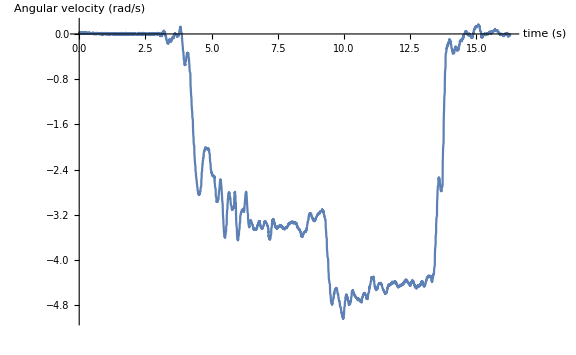

```mathematica
ListLinePlot[spinningData1,AxesLabel->{"time (s)","Angular velocity (rad/s)"},ImageSize->Large]
Export["~/Pictures/spinny1.png",%];
```

```mathematica
getAvgVel[data_,start_,end_]:=Mean[Cases[data,{t_/;(t ≥ start && t ≤ end),x_}:>x]]
```

```mathematica
slow=getAvgVel[spinningData1,6.4,9.1]
```

-3.38082

```mathematica
fast=getAvgVel[spinningData1,9.5,13.3]
```

-4.52409

```mathematica
N[fast/slow,3]
```

1.33816

```mathematica
With[{context="s1`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Spinning Chair 2

```mathematica
With[{context="s2`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
spinningData=Import["data/spinny chair 2.csv","Data"][[2;;All,{1,4}]];
```

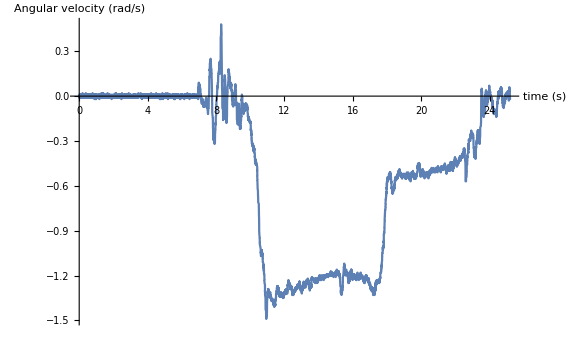

```mathematica
ListLinePlot[spinningData,AxesLabel->{"time (s)","Angular velocity (rad/s)"},ImageSize->Large]
Export["~/Pictures/spinny2.png",%];
```

```mathematica
getAvgVel[data_,start_,end_]:=Mean[Cases[data,{t_/;(t ≥ start && t ≤ end),x_}:>x]]
```

```mathematica
fast=getAvgVel[spinningData,11,17.4]
```

-1.25144

```mathematica
slow=getAvgVel[spinningData,18.3,22.3]
```

-0.507255

```mathematica
N[fast/slow,3]
```

2.46708

```mathematica
(1.4-1.25)/1.25
```

0.12

```mathematica
With[{context="s2`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Scratch Work

```mathematica
exportNotebookPDF[]
```